```mathematica
alpha = 1 Degree
beta = 2 Degree
Expand[Cos[alpha + beta]]
```

°

2 °

Cos[3 °]

```mathematica
Expand[(x+3)(x+2)]
```

6+5 x+x^2

```mathematica
Expand[ax^2+bx+c]
```

ax^2+bx+c

```mathematica
Expand[(1+x)^3(5x^2+1)(x^5+1)]
```

1+3 x+8 x^2+16 x^3+15 x^4+6 x^5+3 x^6+8 x^7+16 x^8+15 x^9+5 x^10

```mathematica
Pi
```

π

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
x = N[Pi,100]*N[Pi,100]
```

9.86960440108935861883449099987615113531369940724079062641334937622004482241920524300177340371855223

```mathematica
Sqrt[x]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

### 傅里叶变换

```mathematica
Clear[{t}]
t = Table[tau, {tau, 0, 1, 0.01}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
x = Sin[2 Pi 10 t] + Sin[2 Pi 20 t]
```

{0.,1.53884,1.53884,0.363271,-0.363271,-1.22465×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-7.34788×10^-16,1.53884,1.53884,0.363271,-0.363271,-3.67394×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-1.46958×10^-15,1.53884,1.53884,0.363271,-0.363271,-6.12323×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-2.20436×10^-15,1.53884,1.53884,0.363271,-0.363271,2.69546×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-2.93915×10^-15,1.53884,1.53884,0.363271,-0.363271,-1.10218×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-3.67394×10^-15,1.53884,1.53884,0.363271,-0.363271,-4.89983×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-4.40873×10^-15,1.53884,1.53884,0.363271,-0.363271,1.96067×10^-15,0.363271,-0.363271,-1.53884,-1.53884,1.61728×10^-14,1.53884,1.53884,0.363271,-0.363271,-5.38968×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-5.8783×10^-15,1.53884,1.53884,0.363271,-0.363271,1.47081×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-6.61309×10^-15,1.53884,1.53884,0.363271,-0.363271,-5.87954×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-7.34788×10^-15}

```mathematica
X = Fourier[x, tau, ω]
```

Fourier::nonopt: Options expected (instead of ω) beyond position 2 in Fourier[{0.,1.53884,1.53884,0.363271,-0.363271,-1.22465×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-7.34788×10^-16,1.53884,«27»,-1.53884,-2.93915×10^-15,1.53884,1.53884,0.363271,-0.363271,-1.10218×10^-15,0.363271,-0.363271,-1.53884,-1.53884,«51»},tau,ω]. An option must be a rule or a list of rules.

Fourier[{0.,1.53884,1.53884,0.363271,-0.363271,-1.22465×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-7.34788×10^-16,1.53884,1.53884,0.363271,-0.363271,-3.67394×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-1.46958×10^-15,1.53884,1.53884,0.363271,-0.363271,-6.12323×10^-16,0.363271,-0.363271,-1.53884,-1.53884,-2.20436×10^-15,1.53884,1.53884,0.363271,-0.363271,2.69546×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-2.93915×10^-15,1.53884,1.53884,0.363271,-0.363271,-1.10218×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-3.67394×10^-15,1.53884,1.53884,0.363271,-0.363271,-4.89983×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-4.40873×10^-15,1.53884,1.53884,0.363271,-0.363271,1.96067×10^-15,0.363271,-0.363271,-1.53884,-1.53884,1.61728×10^-14,1.53884,1.53884,0.363271,-0.363271,-5.38968×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-5.8783×10^-15,1.53884,1.53884,0.363271,-0.363271,1.47081×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-6.61309×10^-15,1.53884,1.53884,0.363271,-0.363271,-5.87954×10^-15,0.363271,-0.363271,-1.53884,-1.53884,-7.34788×10^-15},tau,ω]

```mathematica
Clear[{t}]
signal = Sin[2 Pi t]
```

Sin[2 π t]

```mathematica
fourierTransform = FourierTransform[signal, t, ω]
```

ⅈ √(π/2) DiracDelta[-2 π+ω]-ⅈ √(π/2) DiracDelta[2 π+ω]

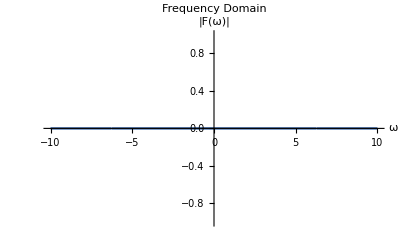

```mathematica
Plot[Abs[fourierTransform], {ω, -10, 10}, PlotRange->All,
PlotLabel->"Frequency Domain", AxesLabel->{"ω", "|F(ω)|"}]
```

```mathematica
inverseTransform = InverseFourierTransform[fourierTransform, ω, t]
```

-1/2 ⅈ ⅇ^(-2 ⅈ π t) (-1+ⅇ^(4 ⅈ π t))

```mathematica
Clear[{t}]
FourierTransform[Exp[-t^2] Sin[t],t,ω]
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

```mathematica
Clear[{t, x, X}]
```

```mathematica
t = Range[0,1,0.01];
x = Sin[2 Pi 5 t]+ 0.5 * Sin[2 Pi 100 t]
```

{0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,2.45053×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,4.4112×10^-15,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,3.79888×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,8.82241×10^-15,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.59452×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,6.12819×10^-15,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.00483×10^-14,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,1.76448×10^-14,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,-2.81421×10^-15,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,7.3974×10^-16}

```mathematica
N[Sum[1/x,{x,1,10000000}]]
```

16.6953

```mathematica
Ceiling[1]
```

1

```mathematica
1 / Ceiling[1]
```

1

```mathematica
Clear[x]
N[Integrate[1/Floor[x] - 1 / x, {x, 1, 1000}]]
```

Integrate::mpwc: Integrate was unable to convert Floor[x] to Piecewise because the required number 1000 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.01261}. NIntegrate obtained 0.60002 and 0.0162193 for the integral and error estimates.

0.60002

```mathematica
Clear[x]
Integrate[2x, {x, 1, 10}]
```

99

```mathematica
Clear[x]
Integrate[1/(1+x)-N[E,10]^-x/x, {x, 1, 100}]
```

3.7025894

```mathematica
Clear[x]
Integrate[1/(1+x)-Power[N[E], -x]/x,{x,1,Infinity}]
```

Integrate::idiv: Integral of -ⅇ^(-1. x)/x+1/(1+x) does not converge on {1,∞}.

∫_1^∞ (-2.71828^-x/x+1/(1+x))ⅆx

```mathematica
Clear[x]
N[Integrate[1/x-Log[1+1/x],{x, 1, Infinity}]]
```

0.386294

```mathematica
Clear[x]
N[Integrate[-1/x+1/Floor[x],{x, 1,1000}]]
```

Integrate::mpwc: Integrate was unable to convert Floor[x] to Piecewise because the required number 1000 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.01261}. NIntegrate obtained 0.60002 and 0.0162193 for the integral and error estimates.

0.60002

```mathematica
Prime[100]
```

541

```mathematica
FactorInteger[100]
```

{{2,2},{5,2}}

```mathematica
For[i = 1, i < 100, ++i, Print[FactorInteger[i]]]
```

{{1,1}}

{{2,1}}

{{3,1}}

{{2,2}}

{{5,1}}

{{2,1},{3,1}}

{{7,1}}

{{2,3}}

{{3,2}}

{{2,1},{5,1}}

{{11,1}}

{{2,2},{3,1}}

{{13,1}}

{{2,1},{7,1}}

{{3,1},{5,1}}

{{2,4}}

{{17,1}}

{{2,1},{3,2}}

{{19,1}}

{{2,2},{5,1}}

{{3,1},{7,1}}

{{2,1},{11,1}}

{{23,1}}

{{2,3},{3,1}}

{{5,2}}

{{2,1},{13,1}}

{{3,3}}

{{2,2},{7,1}}

{{29,1}}

{{2,1},{3,1},{5,1}}

{{31,1}}

{{2,5}}

{{3,1},{11,1}}

{{2,1},{17,1}}

{{5,1},{7,1}}

{{2,2},{3,2}}

{{37,1}}

{{2,1},{19,1}}

{{3,1},{13,1}}

{{2,3},{5,1}}

{{41,1}}

{{2,1},{3,1},{7,1}}

{{43,1}}

{{2,2},{11,1}}

{{3,2},{5,1}}

{{2,1},{23,1}}

{{47,1}}

{{2,4},{3,1}}

{{7,2}}

{{2,1},{5,2}}

{{3,1},{17,1}}

{{2,2},{13,1}}

{{53,1}}

{{2,1},{3,3}}

{{5,1},{11,1}}

{{2,3},{7,1}}

{{3,1},{19,1}}

{{2,1},{29,1}}

{{59,1}}

{{2,2},{3,1},{5,1}}

{{61,1}}

{{2,1},{31,1}}

{{3,2},{7,1}}

{{2,6}}

{{5,1},{13,1}}

{{2,1},{3,1},{11,1}}

{{67,1}}

{{2,2},{17,1}}

{{3,1},{23,1}}

{{2,1},{5,1},{7,1}}

{{71,1}}

{{2,3},{3,2}}

{{73,1}}

{{2,1},{37,1}}

{{3,1},{5,2}}

{{2,2},{19,1}}

{{7,1},{11,1}}

{{2,1},{3,1},{13,1}}

{{79,1}}

{{2,4},{5,1}}

{{3,4}}

{{2,1},{41,1}}

{{83,1}}

{{2,2},{3,1},{7,1}}

{{5,1},{17,1}}

{{2,1},{43,1}}

{{3,1},{29,1}}

{{2,3},{11,1}}

{{89,1}}

{{2,1},{3,2},{5,1}}

{{7,1},{13,1}}

{{2,2},{23,1}}

{{3,1},{31,1}}

{{2,1},{47,1}}

{{5,1},{19,1}}

{{2,5},{3,1}}

{{97,1}}

{{2,1},{7,2}}

{{3,2},{11,1}}

```mathematica
N[Sum[1/x,{x,1,1000000}]]
```

14.3927

```mathematica
N[RandomInteger[{1,9},10] . {10^-1, 10^-2, 10^-3, 10^-4, 10^-5, 10^-6, 10^-7, 10^-8, 10^-9, 10^-10},10]
```

0.9369867134

100

1000

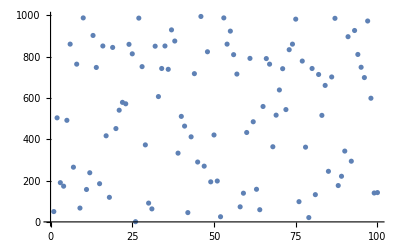

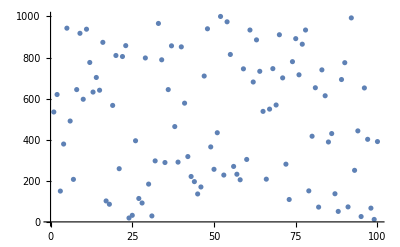

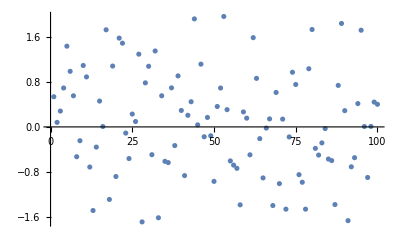

-Graphics-

```mathematica
totalCount = 100
rangeMax = 1000
a = RandomInteger[{1, rangeMax}, totalCount];
(*a = Range[totalCount] * (rangeMax / totalCount)*)
(*For[i=1,i<totalCount,++i,a[[i]]=Sin[a[[i]]]]*)
b = RandomInteger[{1, rangeMax}, totalCount];
c = {};
For[i = 1, i <= totalCount, ++i, c=Append[c, Sin[a[[i]]] +Sin[b[[i]]]]];
(*For[i = 1, i <= totalCount, ++i, c=Append[c, Mod[a[[i]] * b[[i]],rangeMax]]];*)
ListPlot[a]
ListPlot[b]
ListPlot[c]
ArrayPlot[RandomInteger[1, {64,64}]]
```

```mathematica
a = RandomInteger[{1,9},5]
```

{2,9,3,6,3}

```mathematica
b = {}
```

{}

```mathematica
Append[b, a[[1]]]
```

{2}

```mathematica
For[i = 2, i <= 5, ++i, b = Append[b, a[[i]]]]
```

```mathematica
b
```

{9,3,6,3}

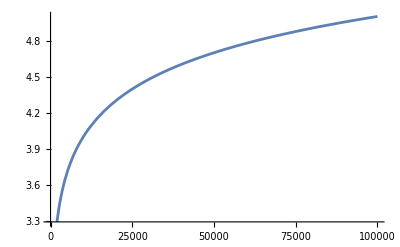

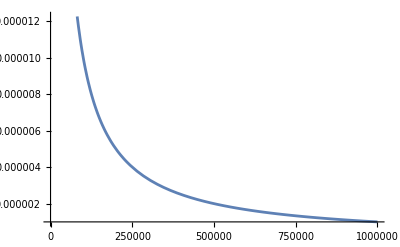

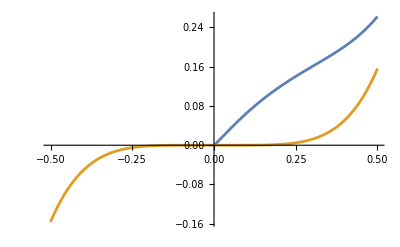

```mathematica
Plot[Log10[x], {x, 0, 100000}]
Plot[1/x, {x, 0, 1000000}]
Plot[{5*x^5.1-4*x^4.1+3*x^3.1-2*x^2.1+x^1.1,5*x^5}, {x, -0.5, 0.5}]
```

```mathematica
(*Define the location:Latitude,Longitude*)latitude=40.7128; (*Example:New York City Latitude*)
longitude=-74.0060; (*Example:New York City Longitude*)

(*Define the date:Year,Month,Day*)
date=DateObject[{2024,12,2}];

(*Use the Sunset function to find the sunset time*)
sunsetTime=Sunset[{latitude,longitude},date]

(*Output the time*)
sunsetTime
```

Mon 2 Dec 2024 05:29:28GMT+8

Mon 2 Dec 2024 05:29:28GMT+8

```mathematica
Sunset[LinguisticAssistant,DateObject[{2023,10,1,0,0},"Minute","Gregorian",-6.]]
```

Mon 2 Oct 2023 07:44:15GMT+8

```mathematica
SunPosition[]
```

{265.237 °,-66.5648 °}

```mathematica
Clear[x]
Integrate[2^x, x]
```

2^x/Log[2]